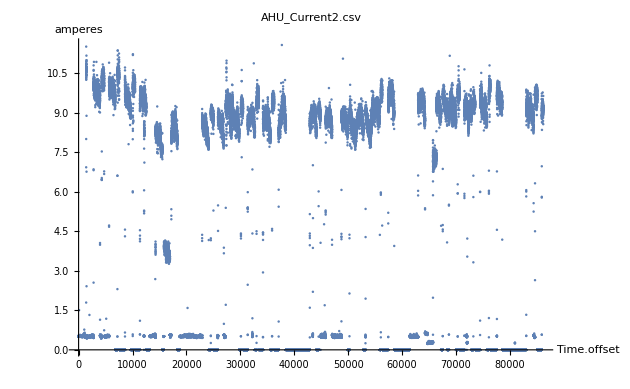

ARMAProcess[0.0247001,{0.123717,0.34381,0.199764,0.294591,0.218851,-0.186326},{0.7879,0.53244,0.388594,0.0982001,-0.112179,0.0587749},0.0742188]

Piecewise[{{19.5993 1.00218^(-1-Abs[s-t])-0.110289 2.20775^(-1-Abs[s-t])+0.000261818 0.806589^Abs[s-t] Cos[2.56828-2.66704 Abs[s-t]]+0.000751778 0.796034^Abs[s-t] Cos[1.30948-1.503 Abs[s-t]], Abs[s-t]>0}, {19.5302, True}}]

8.98579

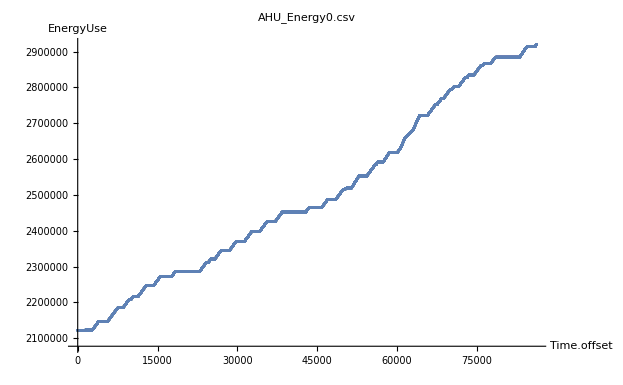

SARIMAProcess[0.000205598,{0.124914},1,{-0.0391605},{1,{},1,{}},0.302502]

2.08656×10^6+0.000318594 x

ARMAProcess[0.0247001,{0.123717,0.34381,0.199764,0.294591,0.218851,-0.186326},{0.7879,0.53244,0.388594,0.0
982001,-0.112179,0.0587749},0.0742188]

Piecewise[{{19.5993 1.00218^(-1-Abs[s-t])-0.110289 2.20775^(-1-Abs[s-t])+0.000261818 0.806589^Abs[s-t] Cos[2.56828-2.66704 Abs[s-t]]+0.000751778 0.796034^Abs[s-t] Cos[1.30948-1.503 Abs[s-t]], Abs[s-t]>0}, {19.5302, True}}]

TimeSeriesForecast[ARMAProcess[0.0247001,{0.123717,0.34381,0.199764,0.294591,0.218851,-0.186326},{0.7879,0.53244,0.388594,0.0982001,-0.112179,0.0587749},0.0742188],data,2]

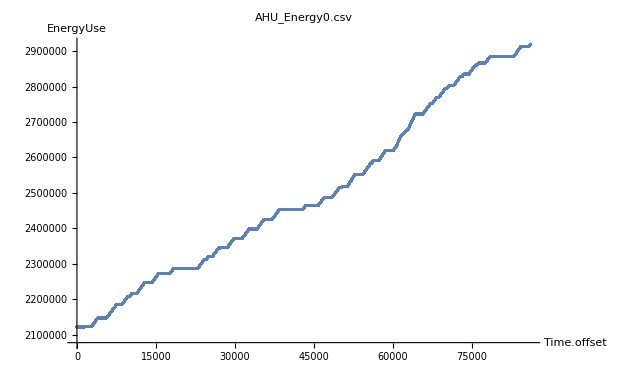

SARIMAProcess[0.000205598,{0.124914},1,{-0.0391605},{1,{},1,{}},0.302502]

2.08656×10^6+0.000318594 x

```mathematica
ClearAll["Global`*"]

fitTimeseriesModel[f_,y_]:=Module[{fname=f,yaxis=y},
dataset=Import[StringJoin["/home/david/Documents/digital-twins/combed.iiitd/datasets/",fname],{"CSV","Data",All,{1,2}},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
time=dataset[[All,1]];
time=Subtract[time,time[[1]]];
timeseries=TimeSeries[dataset[[All,2]],{time}];
Print[ListPlot[dataset[[All,2]],PlotLabel->fname,AxesLabel->{"Time.offset",yaxis}]];
atsm=TimeSeriesModelFit[timeseries];
process=Normal[atsm];
Print[process];
Print[CovarianceFunction[process,s,t]];
Print[TimeSeriesForecast[process,dataset[[All,2]], 2]];
];
(***********************************************)
fitLinearTimeseriesModel[f_,y_]:=Module[{fname=f,yaxis=y},
dataset=Import[StringJoin["/home/david/Documents/digital-twins/combed.iiitd/datasets/",fname],{"CSV","Data",All,{1,2}},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
time=dataset[[All,1]];
time=Subtract[time,time[[1]]];
timeseries=TimeSeries[dataset[[All,2]],{time}];
Print[ListPlot[dataset[[All,2]],PlotLabel->fname,AxesLabel->{"Time.offset",yaxis}]];atsm=TimeSeriesModelFit[timeseries];
process=Normal[atsm];
Print[process];
model=LinearModelFit[timeseries,x,x];
Print[model["BestFit"]];
Show[ListPlot[timeseries],Plot[model["BestFit"],{x,0,80000}],Frame->True]
(*model["ParameterTable"];*)
];
(***********************************************)
fitTimeseriesModel["AHU_Current2.csv","amperes"];
fitLinearTimeseriesModel["AHU_Energy0.csv","EnergyUse"];
(***********************************************)
```